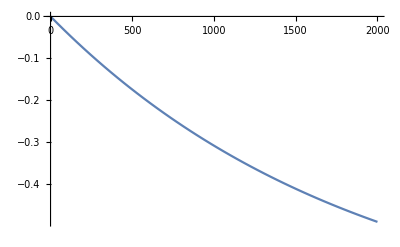

```mathematica
(* Here's the spin 1/2 case using level populations *)
ClearAll["Global`*"];
pe0=-1;
pn0=0;
nt=1;
et=c;
nmDot=(-nm[t]c ep[t]/et(α+θ(1+pn0)+σ(1-pe0+pn0))ω1
-nm[t]c em[t]/et(β+θ(1+pn0)+σ(1+pe0+pn0))ω1
+np[t]c ep[t]/et(β+θ(1-pn0)+σ(1-pe0-pn0))ω1
+np[t]c em[t]/et(α+θ(1-pn0)+σ(1+pe0-pn0))ω1);
npDot=-nmDot;
epDot=(-ep[t] nm[t]/nt(s+α+1-pe0+σ(1-pe0+pn0))ω1
-ep[t] np[t]/nt(s+β+1-pe0+σ(1-pe0-pn0))ω1
+em[t] np[t]/nt(s+α+1+pe0+σ(1+pe0-pn0))ω1
+em[t] nm[t]/nt(s+β+1+pe0+σ(1+pe0+pn0))ω1);
emDot=-epDot;
eqns={np'[t]==npDot,nm'[t]==nmDot,ep'[t]==epDot,em'[t]==emDot,
nm[0]==np[0]==nt/2,ep[0]==0,em[0]==et};
sol=ParametricNDSolve[eqns,{np,nm,ep,em},{t,0,2000},{α,β,s,θ,σ,ω1,c}];
cc=1*^-5;
Plot[(np[3,0,0,0.2,0,33,cc][t]-nm[3,0,0,0.2,0,33,cc][t])/nt/.sol,{t,0,2000},PlotRange->All]
```